```mathematica
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Lynx paper notebook 2

## Script for analysis presented with respect to bee flights

Karem Solanao Sanchez^1, Luis Robledo Ospina^(1,2) and Dinesh Rao^(1*)

1. Inbioteca, Universidad Veracruzana
2. School of Natural Sciences, Macquarie University
1*. vrao@uv.mx

## Preprocessing

### Load Trajectory3D package

Package available at Github, download and move to the Applications subdirectory of your user base directory.

```mathematica
$UserBaseDirectory
```

```mathematica
Needs["Trajectory3D`"]
Names["Trajectory3D`*"]
```

{AngleofFlight,CollettPlot3D,DistanceProfile3D,GetData3D,InputUserValues3D,OrthogonalComponentsVelocity3D,ProximityCut3D,SpeedCollettPlot3D,SpeedProfile3D,TwinCollettPlot3D}

```mathematica
{"AngleofFlight","CollettPlot3D","DistanceProfile3D","GetData3D","InputUserValues3D","OrthogonalComponentsVelocity3D","ProximityCut3D","SpeedCollettPlot3D","SpeedProfile3D","TwinCollettPlot3D"}
```

{AngleofFlight,CollettPlot3D,DistanceProfile3D,GetData3D,InputUserValues3D,OrthogonalComponentsVelocity3D,ProximityCut3D,SpeedCollettPlot3D,SpeedProfile3D,TwinCollettPlot3D}

### Import Data

project specific constants and other variables

```mathematica
fps = 1/500;(*frame rate*)
beefolder = "/Users/dinesh/Dropbox/projects/lynx/lynx prey response/Data/processed data/beedata"; (*insert folder path to csv files *)
bdata=Import[#,"CSV"]&/@FileNames["*.csv",beefolder];
bflights=Range@Length@bdata
```

{1,2,3,4,5,6,7,8,9,10,11,12}

#### Segment trajectory to closest approach to flower (point chosen visually)

```mathematica
SpecialProximityCut3Db[file_,n_]:=Module[{head,obj,cuts,cuttraj},
head=file[[All,{1,2,3}]];
obj=file[[All, {7,8,9}]];
cuts={56,128,67,261,168,374,176,193,32,75,313,144};
cuttraj=file[[;;cuts[[n]],All]];
cuttraj
]
```

```mathematica
bmpc =SpecialProximityCut3Db[bdata[[#]],#]&/@bflights;
```

## Analyses

### Minimum distance

Yellows vs whites

```mathematica
Min[DistanceProfile3D[bmpc[[#]]]]&/@bflights
```

{34.2263,7.88898,5.964,3.50584,6.51213,4.50407,3.97183,5.75997,11.6021,9.81431,0.617638,3.46956}

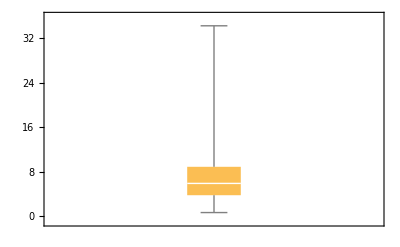

```mathematica
BoxWhiskerChart[{34.226315377020335,7.888978167761659,5.964004926808828,3.5058378972434334,6.512131057704477,4.504065019064763,3.9718338812858427,5.759968277171339,11.602053171043389,9.814311707284112,0.6176380540713232,3.4695607473188677}]
```

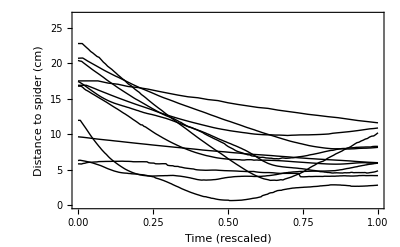

```mathematica
ListLinePlot[N@TimeSeriesRescale[DistanceProfile3D[bmpc[[#]]], {0,1}]&/@bflights, PlotStyle->Directive[{Black, Thin}], Frame->{{True,False},{True,False}},FrameLabel->{{HoldForm["Distance to spider (cm)"],None},{HoldForm["Time (rescaled)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

### Trajectory Plots

Plots of selected trajectories

Ball and pin plot of a typical trajectory

```mathematica
TwinCollettPlot3D[bmpc[[4]]]
```

-Graphics3D-

Colour coded to speed

```mathematica
SpeedCollettPlot3D[bmpc[[4]]]
```

-Graphics3D-

### Distance vs Speed

```mathematica
distspeeds={DistanceProfile3D[bmpc[[#]]],SpeedProfile3D[bmpc[[#]]]}ᵀ&/@bflights;
```

```mathematica
SmoothDensityHistogram[Flatten[distspeeds,1],PlotRange->{{0,30},{0,200}},FrameLabel->{{HoldForm["Speed (cm/s)"],None},{HoldForm["Distance from spider (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

### Persistence Velocity

#### All flights

Extract persistent velocity values for flights

```mathematica
PVbees=OrthogonalComponentsVelocity3D[bmpc[[#]]][[1]]&/@bflights;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Subsample to remove trajectories where computation did not work; standardize (z-score normalisation) and then run a low pass filter

```mathematica
bpv = LowpassFilter[PVbees[[#]],0.5]&/@bflights;
```

Distances for yellow flower flights

```mathematica
bdis=DistanceProfile3D[bmpc[[#]]]&/@bflights;
```

Join to a single dataset

```mathematica
bdistPV = {bdis[[#]][[2;;]],bpv[[#]]}ᵀ&/@{1,2,3,4,5,6,7,8,9,10};
```

Smooth density histogram with contours

```mathematica
SmoothDensityHistogram[Flatten[bdistPV,1],PlotRange->{{0,25},{-100,100}}, Mesh->30,FrameLabel->{{HoldForm[ "Persistence Velocity (cm/s)"],None},{HoldForm["Distance from spider (cm)"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-